# Leads connected to 1 - 10 and 1 to 10

# a1 and a2

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
leads[25]
```

{{{0.-0.848854 ⅈ,0.500319+0. ⅈ,0.+0.170564 ⅈ,-0.00148296+0. ⅈ,0.+0.0219777 ⅈ,0.00302035+0. ⅈ,14,0.+0.000184309 ⅈ,4.2504×10^-6+0. ⅈ,0.+0.000109971 ⅈ,-1.79988×10^-6+0. ⅈ,0.+0.0000334653 ⅈ},23,{1}},299,{1}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Table[{x,25},{x,1,50,1}]
```

{{1,25},{2,25},{3,25},{4,25},{5,25},{6,25},{7,25},{8,25},{9,25},{10,25},{11,25},{12,25},{13,25},{14,25},{15,25},{16,25},{17,25},{18,25},{19,25},{20,25},{21,25},{22,25},{23,25},{24,25},{25,25},{26,25},{27,25},{28,25},{29,25},{30,25},{31,25},{32,25},{33,25},{34,25},{35,25},{36,25},{37,25},{38,25},{39,25},{40,25},{41,25},{42,25},{43,25},{44,25},{45,25},{46,25},{47,25},{48,25},{49,25},{50,25}}

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,25]],concentration],RandomSample[Join[s[1,50,26,50]],total-concentration]],First],10000]
```

```mathematica
dist[50,10][[1]]
```

{{1,44},{2,27},{2,41},{3,31},{5,12},{5,42},{7,33},{8,29},{9,40},{9,43},{12,38},{14,29},{17,46},{19,46},{20,27},{21,36},{21,42},{23,42},{24,34},{24,37},{25,28},{25,49},{26,20},{27,34},{28,35},{28,39},{28,50},{29,21},{29,35},{29,46},{30,9},{30,41},{31,33},{31,47},{32,43},{34,49},{35,26},{35,31},{37,1},{38,9},{38,27},{39,7},{39,35},{40,18},{40,50},{45,28},{46,21},{46,48},{49,30},{50,24}}

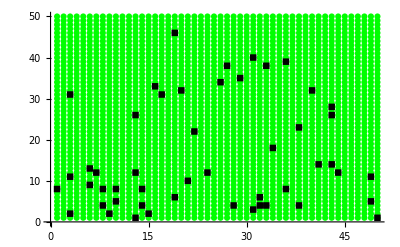

```mathematica
ListPlot[{Join[s[1,50,1,50]],dist[50,30][[1]]},PlotMarkers->Automatic,PlotStyle->{Green,Black}]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=25},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,25}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=25},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:= Module[{sizeoflead=25,abc=dist[total,concentration][[number]]},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

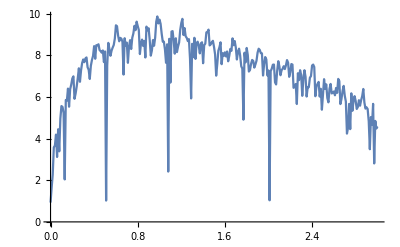

```mathematica
ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,0,50,25,1]},{ω,Range[0,3,0.01]}]]
```

```mathematica
Table[Export["~/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_25_and_1_25/up_down/1_2/ϵ1_conc_"<>ToString[conc]<>"_.dat",Print[conc];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,50,conc,n],{n,500}]]},{ω,Range[0,3,0.01]}]],{conc,40,45,5}]
```

40

45

{~/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_25_and_1_25/up_down/1_2/ϵ1_conc_40_.dat,~/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_25_and_1_25/up_down/1_2/ϵ1_conc_45_.dat}

```mathematica
transmission = Table[{x,Import["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_25_and_1_25/up_down/1_2/ϵ1_conc_"<>ToString[x]<>"_.dat"]},{x,5,45,5}]
```

{{5,{{0.,24.8617},{0.01,26.326},{0.02,15.6873},{0.03,8.85938},{0.04,7.88855},{0.05,8.9398},289,{2.95,3.93701},{2.96,4.1757},{2.97,4.16385},{2.98,4.44959},{2.99,4.48419},{3.,4.50691}}},7,{45,{1}}}
 |  |  |  |

```mathematica
CA[1,0.0001,1,0,1,50,25,1]
```

6.83072

```mathematica
input =Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,50,25,n]},{ω,Range[0,3,0.01]}],{n,100}]
```

{1}
 |  |  |  |

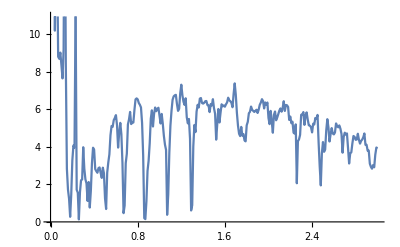

```mathematica
ListLinePlot[input[[2]]]
```

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,9}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
b[Y_,n_]:=Table[misfit[X+Y,X,n][[2]][[1]],{X,Range[0.15,3-Y,0.02]}]
```

```mathematica
b[0.1,1]
```

{10,15,15,15,15,20,20,20,20,20,20,20,25,25,20,15,15,15,15,15,20,20,20,15,15,15,20,20,25,30,35,35,35,30,30,30,25,25,25,25,30,30,25,25,20,20,15,15,15,15,15,15,15,15,20,20,20,20,15,15,15,15,15,20,25,30,35,40,35,30,25,25,25,25,25,20,25,25,25,25,25,20,15,20,20,20,20,20,15,15,20,15,15,15,20,20,20,20,20,25,30,30,25,25,20,15,15,20,20,20,20,20,20,10,15,15,10,10,10,10,15,15,25,20,15,15,10,10,10,15,15,20,25,25,20,15,15,15}

```mathematica
Table[Print[n];N[Mean[Abs[Flatten[Table[b[Y,n],{Y,Range[0.01,2,0.1]}]]]]],{n,100}]
```

{20.5969,25.2435,26.3743,19.5105,27.212,17.9843,24.2016,22.5524,23.5681,27.8979,28.0733,42.5131,24.5759,23.1387,22.7984,36.3403,21.6597,26.0707,29.2749,32.0628,25.267,28.822,16.9424,26.5157,16.1073,17.3665,30.6963,20.3403,28.7173,43.1649,39.2435,20.4424,20.9476,28.4346,25.3613,13.2565,25.9686,32.199,19.8351,12.2408,24.2984,22.7539,23.3194,44.0471,16.2592,41.9267,22.2251,21.7356,30.7958,20.4188,22.5366,24.4817,28.0471,20.0314,28.0445,20.1021,26.3272,18.3979,28.7016,31.3979,19.3586,32.1597,20.199,21.3586,16.9476,28.3298,24.0366,25.2304,31.4267,28.7618,24.8246,16.8429,35.0262,25.7199,27.8351,19.0733,39.1466,25.0131,35.2775,27.5052,18.5524,24.2801,19.4058,17.7644,14.6021,26.1649,16.0707,20.3874,33.3168,30.6283,30.178,24.1859,21.9005,30.9084,43.4817,22.0209,27.0995,17.8586,29.2749,17.0864}

```mathematica
Abs[%30-25]/25
```

{0.176126,0.00973822,0.0549738,0.219581,0.0884817,0.280628,0.0319372,0.0979058,0.0572775,0.115916,0.122932,0.700524,0.0169634,0.0744503,0.0880628,0.453613,0.133613,0.0428272,0.170995,0.282513,0.0106806,0.15288,0.322304,0.0606283,0.355707,0.30534,0.227853,0.186387,0.148691,0.726597,0.569738,0.182304,0.162094,0.137382,0.0144503,0.469738,0.0387435,0.287958,0.206597,0.510366,0.0280628,0.0898429,0.0672251,0.761885,0.349634,0.677068,0.110995,0.130576,0.231832,0.183246,0.098534,0.020733,0.121885,0.198743,0.12178,0.195916,0.053089,0.264084,0.148063,0.255916,0.225654,0.286387,0.192042,0.145654,0.322094,0.133194,0.038534,0.00921466,0.257068,0.150471,0.00701571,0.326283,0.401047,0.0287958,0.113403,0.237068,0.565864,0.00052356,0.411099,0.100209,0.257906,0.0287958,0.22377,0.289424,0.415916,0.0465969,0.357173,0.184503,0.33267,0.225131,0.20712,0.0325654,0.123979,0.236335,0.739267,0.119162,0.0839791,0.285654,0.170995,0.316545}

```mathematica
Mean[%32]
```

0.210337

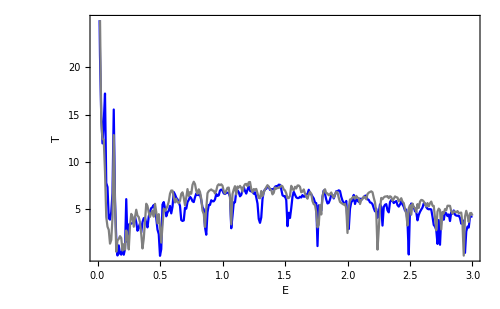

```mathematica
a=(*Manipulate[*)Show[ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,50,25,1]},{ω,Range[0,3,0.01]}],Frame->True,PlotRange->{{0,3},{0,25}},(*Epilog->{Dynamic[If[True,Locator[Dynamic[pt],%20,ImageSize->250],{}]]},*)PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},FrameTicks->{{Range[5,20,5],None},{Automatic,None}}],ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,50,10,1]},{ω,Range[0,3,0.01]}],Frame->True,PlotStyle->{Gray},PlotRange->{{0,3},{0,25}}],FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},ImageSize->500](*,{pt,Scaled[{0.5,0.5}],None}]*)
```

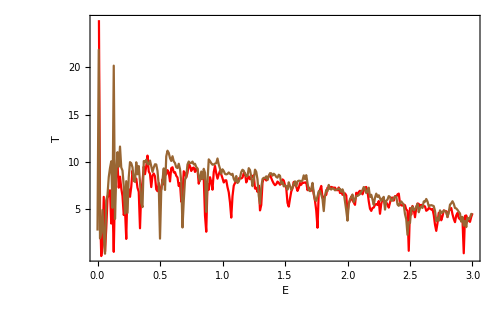

-Graphics-

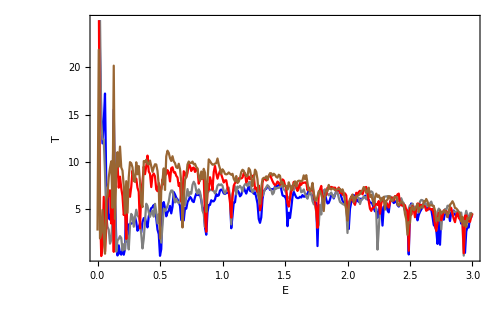

```mathematica
Show[a,%28]
```

```mathematica
300*12
```

3600